```mathematica
NotebookEvaluate[NotebookOpen[StringJoin[NotebookDirectory[],"file-ops.nb"]]];
```

```mathematica
(*** PREDICTIONS ***)
Clear[predPrMonFNRTheor, predFNRfromData, predFPRfromData];

predPrMonFNRTheor[detFPR_, monWin_, pDetNCH0_:0(* for this context *)] := 1 - (1-detFPR)(1 - detFPR - pDetNCH0)^(monWin-1);
```

```mathematica
(*** ANALYSIS ***)
```

```mathematica
Clear[getPrFNRPointEstsWithMonH1ct, getPrFNRPointEstsWithDetH1ct, getPrFNRPointEstResidualsWithH1ct,getPrFnrMSQPairsWithBins];

(* provides a list of triples: (monH1InfoCt, our mon FNR est, data mon FNR est) *) 
getPrFNRPointEstsWithMonH1ct[seshNums_, sampleCtPerSubset_, winSize_ ]:= tallyInfoInTriplesets[({#,predPrMonFNRTheor[predFPRfromData[#, detFilenames], winSize], predFNRfromData[#, monFilenames, winSize,(*monnum*)1]}&/@ sampleAcrossAllSubsets[seshNums, sampleCtPerSubset]), "h1count",monFilenames, winSize,(*monnum*)1];

(* provides a list of triples: (monH1InfoCt, our mon FNR est, data mon FNR est) *) 
getPrFNRPointEstsWithDetH1ct[seshNums_, sampleCtPerSubset_, winSize_ ]:= tallyInfoInTriplesets[({#,predPrMonFNRTheor[predFPRfromData[#, detFilenames], winSize], predFNRfromData[#, monFilenames, winSize,(*monnum*)1]}&/@ sampleAcrossAllSubsets[seshNums, sampleCtPerSubset]), "h1count",detFilenames, winSize, (*monnum*)1];


(* provides a list of absolute residuals for above: (h1InfoCt, abs residual for our mon FNR est, abs residual for data mon FNR est) *) 
getPrFNRPointEstResidualsWithH1ct[seshNums_, sampleCtPerSubset_, winSize_] := With[{gtValue=predPrMonFNRTheor[0.1, winSize]},({#[[1]], Abs[#[[2]]-gtValue],Abs[#[[3]]-gtValue]  } & /@ getPrFNRPointEstsWithMonH1ct[seshNums, sampleCtPerSubset, winSize])];



(* privides a list of (bin start, bin elem count, mean squared error for our appr, mean squared error for data appr) ; bin end determined by bin size *) 
getPrFnrMSQPairsWithBins[seshNums_, sampleCtPerSubset_, winSize_, binSize_]:= With[{h1CtTwoEstList= (*a list of triples (h1ct, our est, data est *) getPrFNRPointEstResidualsWithH1ct[seshNums, sampleCtPerSubset, winSize] },
(* convert h1cts into bin starts *) Flatten[#]&/@Transpose[{(Range[0,  Max@h1CtTwoEstList[[All,1]], binSize]),({Length@#, Mean@(#[[All,2]]^2), Mean@(#[[All,3]]^2)} &/@ binListsBy[h1CtTwoEstList, {First, 0, Max@h1CtTwoEstList[[All,1]]+binSize-1, binSize}])}]];
```

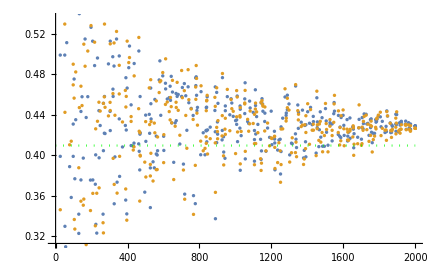

```mathematica
(*** PLOTS PRE CORRECTION ***) 

(* exact estimates plots *) 
(* win = 5 idk what's happening here *) 
With[{data=getFNRPointEstsWithH1ct[{4,5,6,7}, 5, 5]},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]}], chartHorLine[predMonFNRTheor[0.1, 5], Max@data[[All,1]]]]]
```

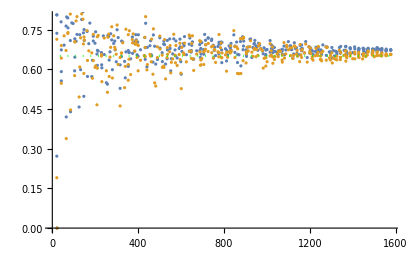

```mathematica
(* win = 10, more or less as expected *) 
With[{data=getFNRPointEstsWithH1ct[{4,5,6,7}, 5, 10]},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]}], chartHorLine[predMonFNRTheor[0.1, 10], Max@data[[All,1]]]]]
```

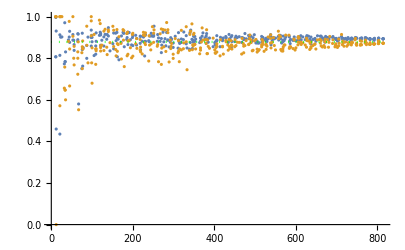

```mathematica
(* win of 20 *)
With[{data=getFNRPointEstsWithH1ct[{4,5,6,7}, 5, 20]},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]}], chartHorLine[predMonFNRTheor[0.1,20], Max@data[[All,1]]]]]
```

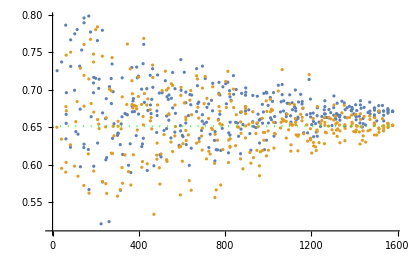
```mathematica
(*** PLOTS POST-CORRECTION ***) 

With[{data=getPrFNRPointEstsWithDetH1ct[{4,5,6,7}, 5, 10]},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]}], chartHorLine[predPrMonFNRTheor[0.1, 10], Max@data[[All,1]]]]]
-Graphics-
```

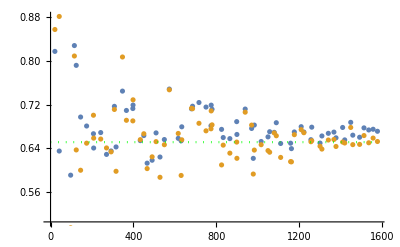

-Graphics-

```mathematica
With[{data=getPrFNRPointEstsWithMonH1ct[{4,5,6,7}, (*samples per subset size*)1, (*winsize*)10]},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]}], chartHorLine[predPrMonFNRTheor[0.1, (*winsize*)10], Max@data[[All,1]]]]]
```

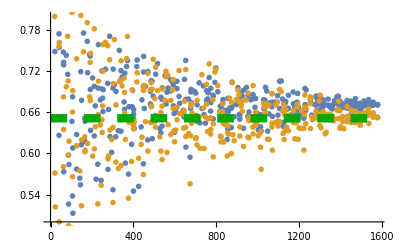

```mathematica
(* PRODUCTION-READY PAPER EST PLOT *) 
plotPrFnr= With[{data=getPrFNRPointEstsWithMonH1ct[{4,5,6,7}, 5, 10]},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]},PlotRange->{0.5,0.8}, PlotMarkers->{"OpenMarkers", Large}], chartHorLine[predPrMonFNRTheor[0.1, 10], Max@data[[All,1]],0, Darker@Green, {AbsoluteThickness[6],AbsoluteDashing[12]}]]]
```

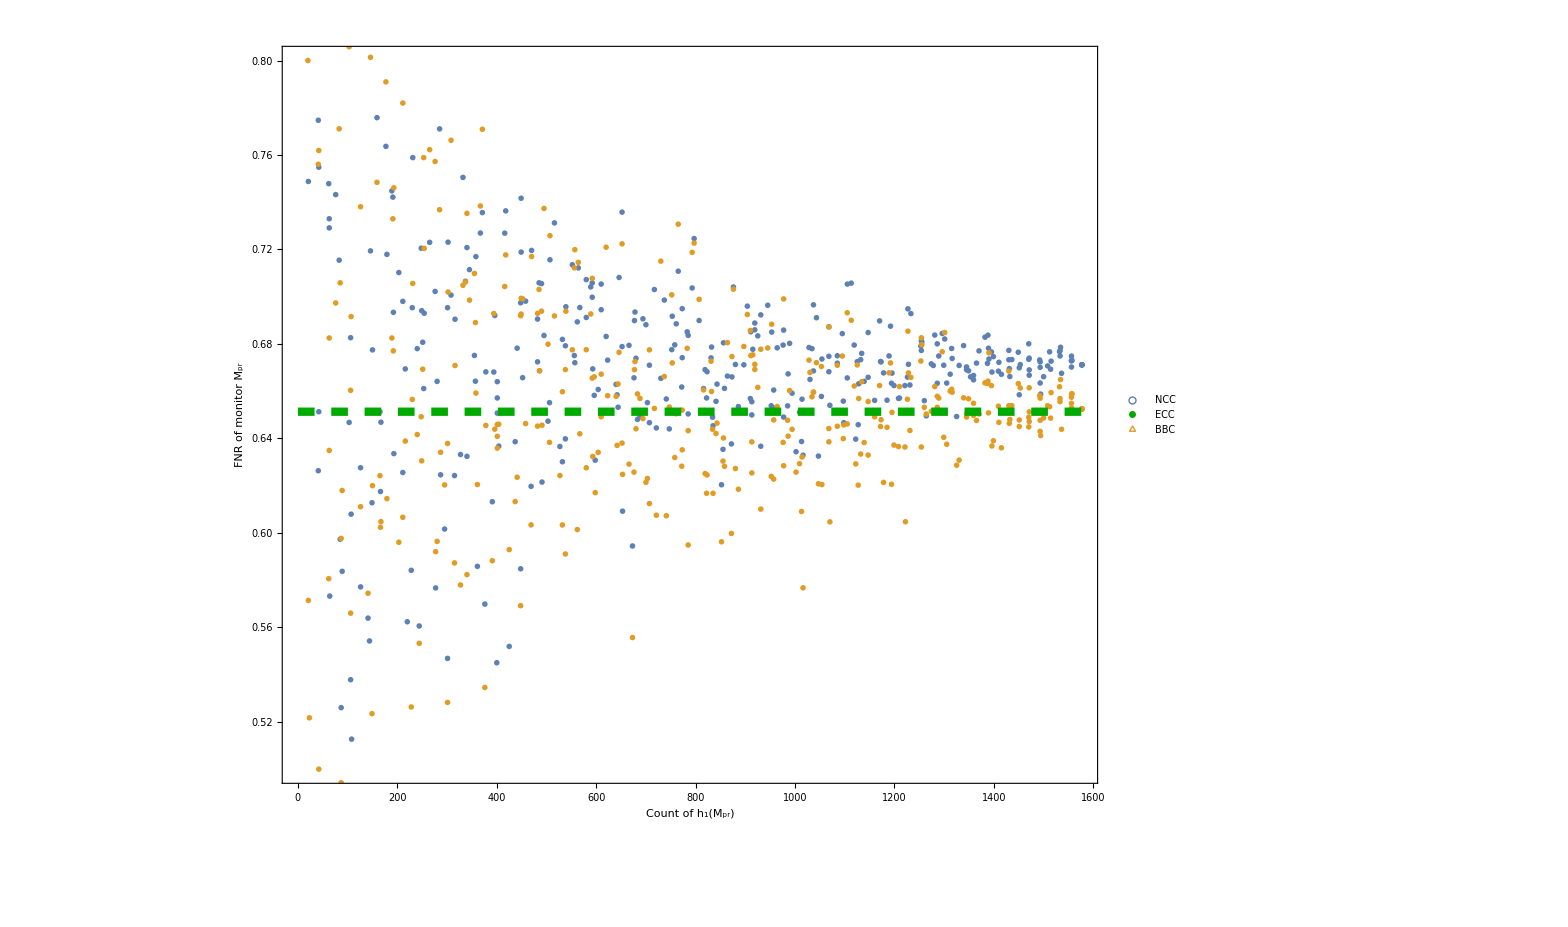

```mathematica
plotPrFnrLegended = Legended[Show[plotPrFnr, Frame->True, FrameLabel->{StringJoin["Count of ", ToString[ Style[StringJoin[ToString[Subscript[ "h", "1"],StandardForm], "(",ToString[Subscript[ "M", "pr"],StandardForm] ,")"], Italic], StandardForm] ],StringJoin["FNR of monitor ", ToString[Style[Subscript[ "M", "pr"],Italic], StandardForm]]}, ImageSize->1500, BaseStyle-> {FontSize->35}], Placed[PointLegend[Directive@@@{{ColorData[97,"ColorList"][[1]]},{AbsoluteDashing[6],AbsoluteThickness[4],Darker@Green} , {ColorData[97,"ColorList"][[2]]}},{"NCC","ECC", "BBC"},
LegendMarkerSize->20,LegendMarkers->{Style[○,Bold,FontSize->28] , Graphics[{Line[{{-10,0},{10,0}}]}],Style[△,Bold,FontSize->28] (*Graphics[{Thick,SSSTriangle[1,1,1]}]*)}],{0.9,0.2}]]
```

```mathematica
(*** RESIDUAL PLOTS PRE CORRECTION  ***)
```

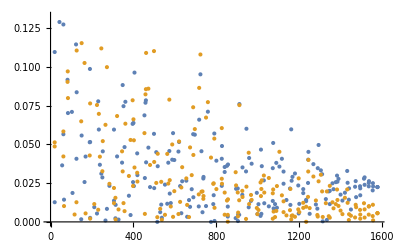

```mathematica
(* monwin = 10 *) 
With[{data=getFNRPointEstResidualsWithH1ct[{4,5,6,7}, 3, 10]},ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]}]]
```

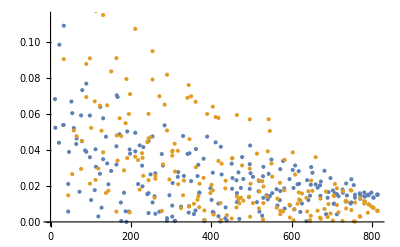

```mathematica
(* monwin = 20 *) 
With[{data=getFNRPointEstResidualsWithH1ct[{4,5,6,7}, 3, 20]},ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]}]]
```

```mathematica
(** MSE BINNED PRE CORRECTION *)
```

{{0,8,0.00573299,0.0330287},{100,9,0.00508724,0.0104951},{200,10,0.00411304,0.00541601},{300,9,0.00214534,0.00167997},{400,9,0.000746607,0.00124988},{500,9,0.000457571,0.000852869},{600,10,0.00117991,0.00148944},{700,10,0.000861455,0.000839186},{800,10,0.00133667,0.000756698},{900,7,0.000372046,0.000659677},{1000,11,0.000481529,0.000245132},{1100,8,0.000462069,0.000337309},{1200,9,0.000522119,0.000209537},{1300,9,0.00054915,0.00014349},{1400,10,0.000384354,0.000069796},{1500,8,0.000477974,0.0000411412}}

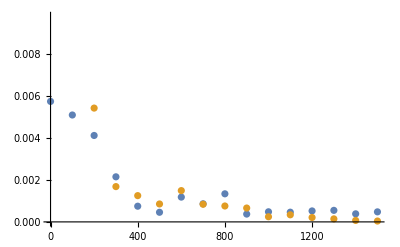

```mathematica
getFnrMSQPairsWithBins[(* sessions *){4,5,6,7}, (*samples per subset size*)2,(*win size *)  10, (* bin width *)100]
ListPlot[{%[[All,{1,3}]], %[[All,{1,4}]]}]
```

{{0,2,0.015015,0.0685941},{25,2,0.0179207,0.0179192},{50,2,0.0227079,0.0330672},{75,2,0.0282738,0.0176231},{100,3,0.00709246,0.00827897},{125,3,0.00376295,0.00294735},{150,2,0.0013056,0.011709},{175,1,0.00127658,0.0145683},{200,3,0.00893971,0.0199228},{225,2,0.00171752,0.00171121},{250,2,0.00410466,0.00303521},{275,2,0.00067939,0.00541707},{300,3,0.00264012,0.0066568},{325,1,0.0357496,0.0103575},{350,3,0.00182502,0.000712011},{375,3,0.00190722,0.00286232},{400,2,0.00267552,0.00683221},{425,2,0.0000280041,0.000108336},{450,2,0.000494783,0.000925432},{475,4,0.00225959,0.00244195},{500,2,0.000850907,0.000891284},{525,2,0.00401037,0.00663378},{550,3,0.000903833,0.00149883},{575,2,0.00246607,0.00481178},{600,2,0.000287611,0.000293846},{625,1,0.00218306,0.00376926},{650,4,0.0016582,0.000744897},{675,1,0.00226162,0.00141616},{700,3,0.00219151,0.00262807},{725,2,0.0026002,0.00200301},{750,3,0.000535773,0.000199106},{775,2,0.002941,0.000554627},{800,2,0.000414254,0.000121502},{825,2,0.000414566,0.000324575},{850,3,0.00108044,0.000272049},{875,3,0.00186937,0.000358},{900,1,0.0000183256,0.0010115},{925,4,0.000517402,0.000514928},{950,1,2.2578×10^-6,0.00080586},{975,2,0.000617762,0.000300303},{1000,3,0.000793198,0.000494145},{1025,1,4.38287×10^-6,0.000051204},{1050,3,0.00107016,0.000357237},{1075,3,0.00111478,0.00200093},{1100,2,0.0000860983,0.000260459},{1125,3,0.000778408,0.0000876724},{1150,1,0.00171054,0.0000535807},{1175,2,0.000165853,0.0000939689},{1200,5,0.000881672,0.0000896408},{1225,0,Mean[{}]^2,Mean[{}]^2},{1250,3,0.00105606,0.000238201},{1275,2,0.000113878,0.000128965},{1300,3,0.00047892,0.0000583774},{1325,2,0.000792434,0.0000560931},{1350,2,0.000125127,0.0000876571},{1375,2,0.000517983,0.0000329356},{1400,4,0.000371308,0.0000203296},{1425,1,0.000526636,1.54833×10^-6},{1450,3,0.000288138,0.0000331507},{1475,2,0.000782735,0.000285993},{1500,2,0.000392143,8.82902×10^-7},{1525,2,0.000570496,0.000169984},{1550,2,0.000434134,0.0000313687},{1575,2,0.000505032,0.0000316069}}

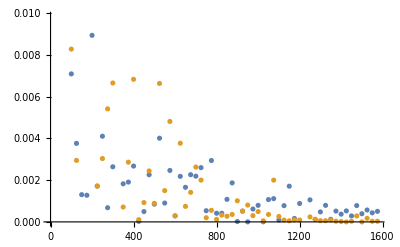

```mathematica
(* bin size 25 *) 
getFnrMSQPairsWithBins[(* sessions *){4,5,6,7},(*samples per subset size*) 2,(*win size *) 10,(* bin width *) 25]
ListPlot[{%[[All,{1,3}]], %[[All,{1,4}]]}]
```

{{0,18,0.0287808,0.0352604},{25,19,0.015943,0.0317375},{50,23,0.0102348,0.0135733},{75,20,0.0110803,0.0213338},{100,23,0.0101274,0.015257},{125,28,0.00473946,0.00781901},{150,23,0.003506,0.00830084},{175,22,0.00290991,0.00353092},{200,22,0.00323265,0.00439488},{225,18,0.00546214,0.0051658},{250,27,0.00236683,0.00456669},{275,23,0.00280531,0.00307458},{300,26,0.00201102,0.00284838},{325,23,0.00205998,0.00376495},{350,20,0.00226681,0.00438053},{375,26,0.00237569,0.00190615},{400,20,0.00136152,0.00283017},{425,25,0.00115502,0.00227449},{450,26,0.0018339,0.0020331},{475,23,0.000671643,0.00107462},{500,26,0.00144348,0.00173275},{525,18,0.000733422,0.00103032},{550,21,0.000593297,0.000602753},{575,26,0.000878977,0.00115957},{600,21,0.000741893,0.0011994},{625,27,0.00132953,0.00174241},{650,18,0.000821229,0.000901095},{675,28,0.000857846,0.000984705},{700,22,0.000783761,0.00126478},{725,21,0.000591805,0.00088186},{750,27,0.000621801,0.000640178},{775,18,0.000639936,0.000701685},{800,23,0.000782354,0.000589543},{825,21,0.000592459,0.000395174},{850,24,0.000939264,0.000742939},{875,27,0.000693275,0.000509967},{900,21,0.000863451,0.000771834},{925,28,0.000567743,0.000454366},{950,23,0.000738062,0.000438153},{975,18,0.000462103,0.000429456},{1000,24,0.000619795,0.000400701},{1025,27,0.000605447,0.000376875},{1050,23,0.000585451,0.00064715},{1075,19,0.000937552,0.000592697},{1100,27,0.000750234,0.00030754},{1125,22,0.00028044,0.00020575},{1150,23,0.000603704,0.00040483},{1175,22,0.000487612,0.000106188},{1200,21,0.000539888,0.000278555},{1225,26,0.000473016,0.00025495},{1250,24,0.000459401,0.000198423},{1275,19,0.000382904,0.000191851},{1300,25,0.000448099,0.000149785},{1325,26,0.000324194,0.0000734809},{1350,21,0.00042398,0.000154895},{1375,23,0.000452973,0.000106487},{1400,19,0.000591106,0.00016001},{1425,28,0.000440724,0.0000691088},{1450,28,0.000523337,0.000096837},{1475,20,0.000349377,0.0000513649},{1500,20,0.000557949,0.0000688996},{1525,20,0.000586356,0.0000752958},{1550,20,0.000484697,0.0000325504},{1575,20,0.000505032,0.0000316069}}

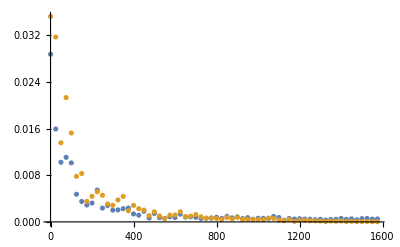

```mathematica
getFnrMSQPairsWithBins[ (* sessions *) {4,5,6,7},(*samples per subset size*)20, (*win size *) 10, (* bin width *)25]
ListPlot[{%[[All,{1,3}]], %[[All,{1,4}]]}, PlotRange->All]
```

{{0,28,0.0375117,0.0491165},{25,30,0.0231945,0.0228987},{50,27,0.0119491,0.0238968},{75,34,0.006877,0.010919},{100,32,0.0067321,0.0132701},{125,48,0.00563631,0.00593393},{150,28,0.00474723,0.00515492},{175,34,0.00542503,0.00714783},{200,36,0.00237584,0.00444382},{225,31,0.0026891,0.00475228},{250,36,0.00257135,0.00410447},{275,37,0.00289447,0.00435525},{300,39,0.00233935,0.00286009},{325,32,0.00246223,0.0044528},{350,31,0.00110965,0.00212359},{375,41,0.00162653,0.00183429},{400,26,0.00180395,0.00228739},{425,45,0.00122952,0.00181191},{450,28,0.00151493,0.00257589},{475,36,0.00117032,0.00164869},{500,35,0.000994081,0.00187824},{525,37,0.000935209,0.00138601},{550,35,0.0012637,0.00106839},{575,34,0.00127906,0.00164129},{600,38,0.000708015,0.000752075},{625,37,0.000676639,0.00106796},{650,32,0.00116569,0.00108009},{675,29,0.00108994,0.0013783},{700,33,0.00131823,0.00120748},{725,41,0.000956545,0.00118011},{750,28,0.000567789,0.000702906},{775,33,0.0006801,0.000464208},{800,35,0.000513536,0.000703578},{825,39,0.000879695,0.000753191},{850,36,0.000895445,0.00113007},{875,37,0.000689687,0.000405081},{900,30,0.000862753,0.000541078},{925,30,0.000752631,0.000568478},{950,40,0.000733071,0.000706349},{975,37,0.0008806,0.000404676},{1000,33,0.00065015,0.000572807},{1025,33,0.000566045,0.000365419},{1050,36,0.000918167,0.000413167},{1075,35,0.000509399,0.000293261},{1100,33,0.000462852,0.000293003},{1125,39,0.000540884,0.00037036},{1150,31,0.000532629,0.000199993},{1175,37,0.000503706,0.000257674},{1200,37,0.000543017,0.000227632},{1225,29,0.000651773,0.000151919},{1250,38,0.000487689,0.000159238},{1275,35,0.000468836,0.000186749},{1300,39,0.000546299,0.000231991},{1325,32,0.000502885,0.000153049},{1350,30,0.000382024,0.000151949},{1375,40,0.000533731,0.000170608},{1400,27,0.000516201,0.000151194},{1425,31,0.000358017,0.0000834137},{1450,50,0.000464131,0.0000865302},{1475,31,0.000498612,0.0000493958},{1500,30,0.000486555,0.0000575775},{1525,29,0.000494029,0.0000388695},{1550,30,0.000511128,0.0000293356},{1575,30,0.000505032,0.0000316069}}

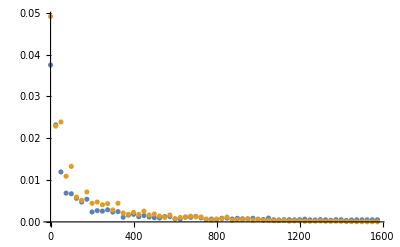

```mathematica
getFnrMSQPairsWithBins[ (* sessions *) {4,5,6,7},(*samples per subset size*)30, (*win size *) 10, (* bin width *)25]
ListPlot[{%[[All,{1,3}]], %[[All,{1,4}]]}, PlotRange->All]
```

```mathematica
getFnrMSQPairsWithBins[ (* sessions *) {4,5,6,7},(*samples per subset size*)40, (*win size *) 10, (* bin width *)25]
```

{{0,34,0.0536262,0.108222},{25,43,0.0111592,0.0240177},{50,41,0.010197,0.0182821},{75,40,0.0102561,0.014248},{100,48,0.00715323,0.0110616},{125,59,0.00452038,0.00784591},{150,39,0.00337882,0.00437757},{175,52,0.00427703,0.00885948},{200,39,0.00238757,0.00554905},{225,44,0.00265323,0.00455688},{250,49,0.00337918,0.00461513},{275,52,0.00247968,0.0043921},{300,41,0.00262488,0.00338961},{325,48,0.00155941,0.00142563},{350,41,0.00166129,0.00239217},{375,50,0.00148623,0.00207956},{400,47,0.00218306,0.00267578},{425,43,0.00212309,0.00258198},{450,50,0.00179435,0.00160826},{475,48,0.00149227,0.00160334},{500,42,0.00134952,0.000985379},{525,47,0.00156646,0.00187621},{550,49,0.000950152,0.000940954},{575,43,0.00116856,0.00120504},{600,44,0.00178096,0.00146753},{625,55,0.0010249,0.00131442},{650,39,0.000795405,0.00103052},{675,46,0.000806045,0.00124711},{700,49,0.000711594,0.00124239},{725,47,0.000683407,0.000659227},{750,42,0.000459569,0.000562186},{775,47,0.000838913,0.00112921},{800,49,0.000652218,0.000841056},{825,47,0.000761032,0.00101885},{850,42,0.000799099,0.000465263},{875,55,0.000692028,0.000407844},{900,45,0.000547208,0.000533389},{925,42,0.000570198,0.000309779},{950,37,0.000499833,0.000434428},{975,55,0.000748284,0.00041743},{1000,45,0.000462384,0.000412755},{1025,48,0.000620885,0.000452507},{1050,51,0.000790648,0.000442585},{1075,40,0.000513062,0.000375775},{1100,47,0.000533365,0.000351174},{1125,43,0.000529013,0.000423294},{1150,51,0.000461589,0.000341414},{1175,44,0.000552237,0.000176245},{1200,47,0.000574433,0.000234907},{1225,50,0.000486922,0.00020478},{1250,45,0.000570713,0.000257172},{1275,51,0.000525437,0.000127957},{1300,44,0.000427004,0.0000959844},{1325,49,0.000476387,0.000134131},{1350,42,0.000559725,0.000138882},{1375,46,0.000528888,0.00010332},{1400,42,0.000474655,0.0000390192},{1425,41,0.000469497,0.000101004},{1450,64,0.000474749,0.0000771256},{1475,41,0.000556576,0.0000581684},{1500,42,0.000554852,0.0000664518},{1525,41,0.000504471,0.0000392841},{1550,36,0.000507123,0.000029429},{1575,40,0.000505032,0.0000316069}}

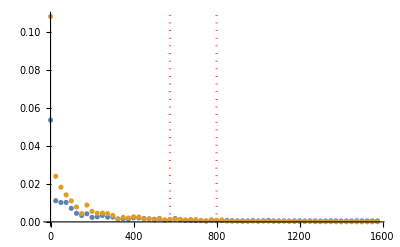

```mathematica
Show[ListPlot[{%482[[All,{1,3}]], %482[[All,{1,4}]]}, PlotRange->All], chartVertLine[575, 0.15, 0, Red], chartVertLine[800, 0.15, 0, Red]]
```

```mathematica
(* a mean NON-squared error *) 
getFnrMSQPairsWithBins[ (* sessions *) {4,5,6,7},(*samples per subset size*)40, (*win size *) 10, (* bin width *)25]
```

{{0,39,0.223983,0.237494},{25,35,0.134325,0.145269},{50,44,0.10847,0.13423},{75,40,0.0880091,0.118525},{100,44,0.0766619,0.105554},{125,56,0.0708176,0.0926714},{150,50,0.0793585,0.0940481},{175,44,0.0578664,0.0700379},{200,43,0.0492021,0.0693916},{225,41,0.0459677,0.0586321},{250,54,0.0517919,0.0616602},{275,48,0.0420567,0.0575552},{300,44,0.0501414,0.0570672},{325,47,0.0488217,0.0512913},{350,43,0.0469325,0.0513957},{375,44,0.0448065,0.0476167},{400,52,0.0414487,0.0529834},{425,41,0.0410866,0.0412648},{450,46,0.0383543,0.0444679},{475,49,0.0312133,0.0422076},{500,48,0.0269758,0.0377266},{525,42,0.0344542,0.0365944},{550,56,0.0311484,0.0476865},{575,39,0.0340125,0.0307858},{600,51,0.0329625,0.0340051},{625,46,0.0348644,0.0360483},{650,46,0.0316876,0.0376947},{675,40,0.0373283,0.0286567},{700,44,0.0300993,0.0347031},{725,51,0.0244635,0.0273661},{750,49,0.0304895,0.0314871},{775,43,0.0284513,0.026815},{800,46,0.0249838,0.024529},{825,44,0.0251087,0.025879},{850,52,0.0296019,0.02787},{875,46,0.0222159,0.0242155},{900,44,0.029315,0.0250729},{925,42,0.0265939,0.0218099},{950,52,0.0220228,0.0208423},{975,43,0.0264051,0.0203542},{1000,46,0.0212991,0.0208532},{1025,50,0.0290322,0.0195589},{1050,41,0.0273667,0.0190814},{1075,47,0.0241451,0.0161176},{1100,50,0.0241854,0.0185459},{1125,43,0.0263281,0.0158673},{1150,49,0.0237476,0.0173019},{1175,43,0.0213392,0.0160894},{1200,53,0.023541,0.014038},{1225,38,0.0208846,0.00972138},{1250,51,0.0239654,0.0150923},{1275,45,0.0235514,0.0160312},{1300,44,0.0232363,0.0165334},{1325,53,0.0206439,0.0109712},{1350,47,0.0246857,0.0117804},{1375,42,0.0233253,0.0105898},{1400,42,0.0201389,0.0106494},{1425,43,0.0220856,0.00976081},{1450,64,0.0227769,0.0100823},{1475,41,0.0219936,0.00696348},{1500,41,0.0214776,0.00820399},{1525,42,0.0224989,0.00632691},{1550,37,0.0222811,0.00558993},{1575,40,0.0224729,0.005622}}

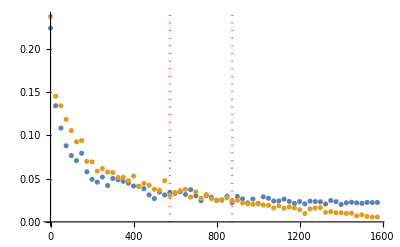

```mathematica
Show[ListPlot[{%491[[All,{1,3}]], %491[[All,{1,4}]]}, PlotRange->All], chartVertLine[575, 0.25, 0, Red], chartVertLine[875, 0.25, 0, Red]]
```

```mathematica
(* MSE BINNED POST CORRECTION *)
```

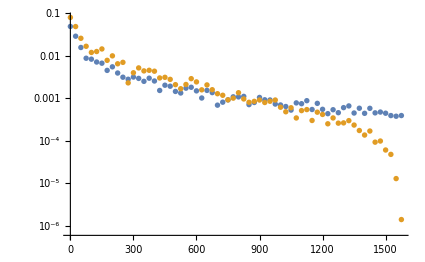

```mathematica
Clear[data];(data = getFnrMSQPairsWithBins[ (* sessions *) {4,5,6,7},(*samples per subset size*)40, (*win size *)10, (* bin width *)25];
ListLogPlot[{data[[All,{1,3}]], data[[All,{1,4}]]}, PlotRange->All])
```

```mathematica
msePrdata={{0,37,0.04952981586725377,0.08066410723325736},{25,39,0.029192055257806528,0.04923302932802642},{50,41,0.015825218705444708,0.026062447255292685},{75,43,0.008832819468686953,0.016891660627116924},{100,42,0.008399909683368343,0.012102439861463532},{125,59,0.007194757024074231,0.012718573562340756},{150,46,0.006751683337828719,0.014612662044876663},{175,46,0.0045708414026471855,0.00788275461886156},{200,45,0.005545420378614478,0.010053420156386694},{225,41,0.003961111314793591,0.006539916472859259},{250,56,0.003157033046428468,0.007067036106172437},{275,42,0.0028244558262652416,0.002320369609163175},{300,44,0.0031858780132528216,0.004015302462463975},{325,50,0.0029590033044487613,0.005226112340331993},{350,42,0.0025241084333276743,0.004445580539431523},{375,49,0.0029913703836566973,0.004592340052171543},{400,45,0.002570723146370012,0.004373628905953624},{425,43,0.001538318071433719,0.0030315271195947226},{450,53,0.002045391966911909,0.0031364015302981015},{475,46,0.0019365376086748292,0.0028088446808885066},{500,42,0.0014592183512067587,0.002107653224709117},{525,51,0.001341371362625275,0.0016886837391206764},{550,43,0.0017430507669453496,0.0021258561333038603},{575,38,0.0018285657674336337,0.002917886615067157},{600,55,0.0015050629410553675,0.0024469924124533595},{625,40,0.0010215495415755345,0.0015916634544455674},{650,57,0.0015437167275312218,0.0020766204299089842},{675,46,0.0013697742156582957,0.0016017216011380271},{700,42,0.0006931744551154653,0.001289696741662015},{725,41,0.0008145325156051515,0.0011852080878589923},{750,48,0.0009248549451518371,0.000924954118537428},{775,51,0.0010893754938180122,0.001014851300808934},{800,47,0.001084668270504051,0.001361125104107679},{825,44,0.0011158267918015613,0.0009704172276652001},{850,44,0.0007135121759537312,0.0008097790199442174},{875,50,0.0008017829658734026,0.0008522204230405637},{900,48,0.0010533711284937523,0.0009159852139075933},{925,47,0.000927366489073891,0.000801434238001634},{950,42,0.0009178366221760056,0.0008566527579464198},{975,45,0.0007358751867999606,0.0009158588485302582},{1000,49,0.0007001600362691018,0.0006194518279350624},{1025,45,0.0006440439026313952,0.0004844283742524315},{1050,48,0.0005304015734245577,0.0006019785217215555},{1075,46,0.000783610735952896,0.000346119752374182},{1100,46,0.00075039155637751,0.000516030907094603},{1125,45,0.0008833946308614716,0.0005452496084047757},{1150,45,0.000547710420728247,0.00030210577652932673},{1175,47,0.0007638798363728501,0.000473455153798869},{1200,49,0.0005534783295272416,0.0004189942527016775},{1225,42,0.000436927498701829,0.00025232551043362226},{1250,45,0.0005410433718373611,0.0003464334902513444},{1275,46,0.00046102234631106924,0.00026126080721817596},{1300,52,0.0006060753983740977,0.00026498645701357535},{1325,50,0.0006646311170644211,0.00029951916278280686},{1350,39,0.00045250101819084625,0.00023553364603813597},{1375,43,0.0005867350132968008,0.0001752055555555938},{1400,48,0.00044511399720745075,0.00013711168512990074},{1425,44,0.0005837792177979779,0.00017039108257076217},{1450,60,0.0004564610659100412,0.00009320009649971713},{1475,42,0.00047706876757147256,0.00009906926432985413},{1500,40,0.0004476947933494785,0.00006085943910686495},{1525,41,0.00039420247530919317,0.00004799459708801235},{1550,38,0.00038014862820101624,0.000012920711210260915},{1575,40,0.000394508636146404,1.3999526929356987*^-6}};
```

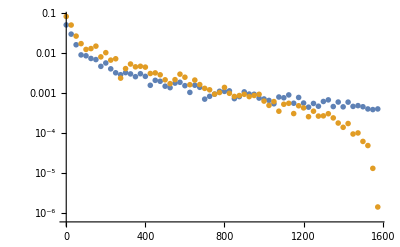

```mathematica
msePrplot = ListLogPlot[{msePrdata[[All,{1,3}]], msePrdata[[All,{1,4}]]}, PlotRange->All, PlotMarkers->{"OpenMarkers", Large}]
```

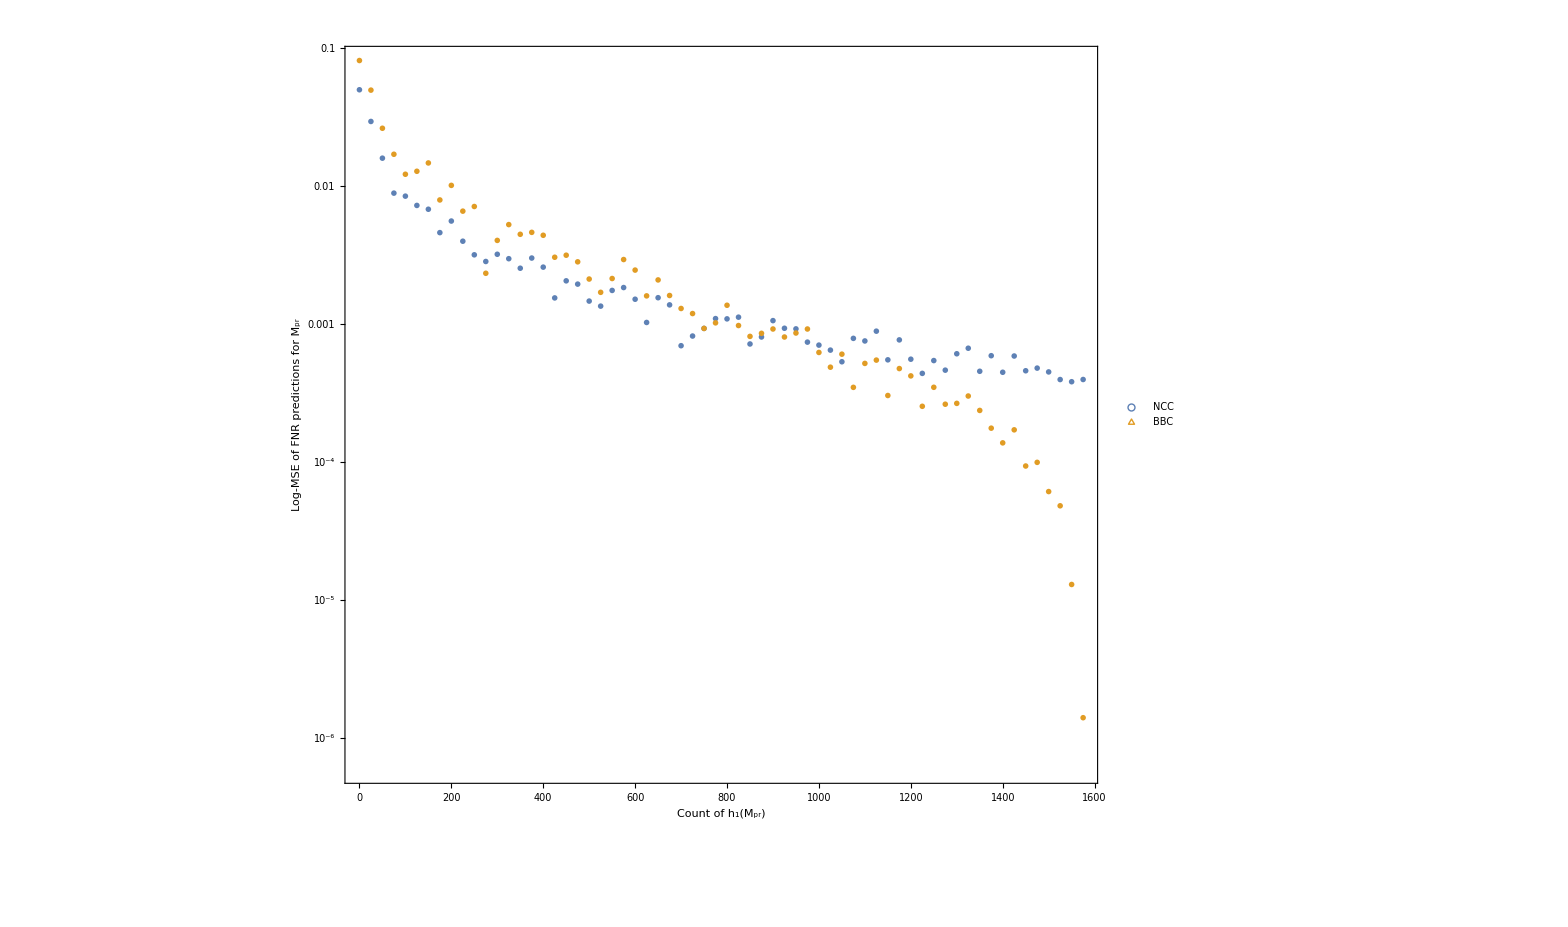

```mathematica
mseRfplotLegended = Legended[Show[msePrplot, Frame->True, FrameLabel->{StringJoin["Count of ", ToString[ Style[StringJoin[ToString[Subscript[ "h", "1"],StandardForm], "(",ToString[Subscript[ "M", "pr"],StandardForm] ,")"], Italic], StandardForm] ], StringJoin["Log-MSE of FNR predictions for ", ToString[Subscript[ "M", "pr"], StandardForm]]}, ImageSize->1500, BaseStyle-> {FontSize->35}],Placed[PointLegend[Directive@@@{{ColorData[97,"ColorList"][[1]]} , {ColorData[97,"ColorList"][[2]]}},{"NCC", "BBC"},
LegendMarkerSize->20,LegendMarkers->{Style[○,Bold,FontSize->28] , Style[△,Bold,FontSize->28] (*Graphics[{Thick,SSSTriangle[1,1,1]}]*)}],{0.1,0.15}]]
```